### The 2-loop ghost selfenergy

```mathematica
$LoadTARCER=True;$LoadFeynArts=True;
```

```mathematica
<<HighEnergyPhysics`FeynCalc`
```

Loading FeynCalc from /home/rolfm/HighEnergyPhysics

Loading TARCER /home/rolfm/HighEnergyPhysics/Tarcer/tarcerLinuxx8664bit25.mx

FeynCalc 8.1.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

Loading FeynArts, see www.feynarts.de for documentation

FeynArts 3.4 patched for use with FeynCalc

#### The graphs

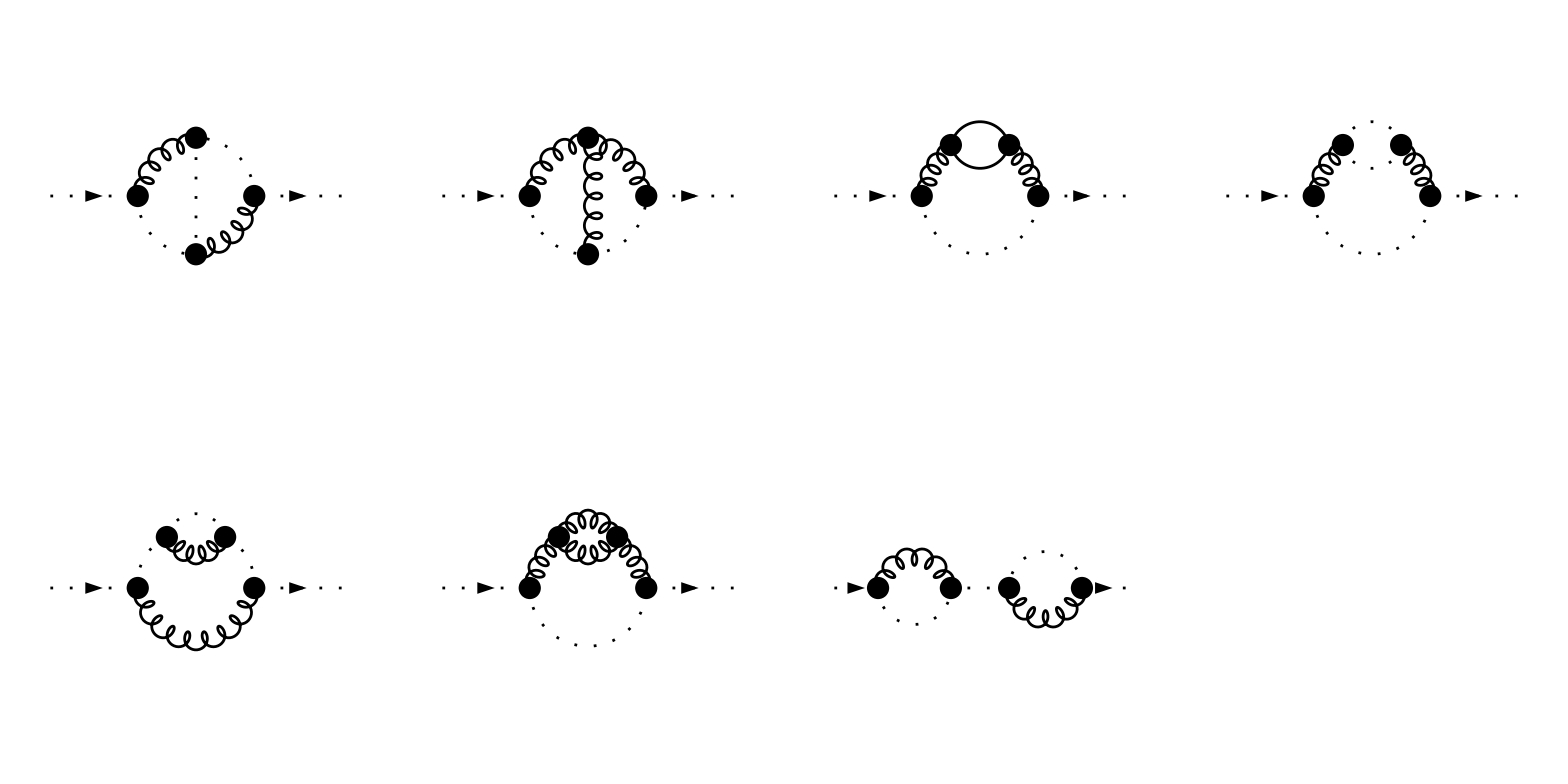

```mathematica
Paint[inserts=InsertFields[Rest@CreateTopologies[2,1->1,ExcludeTopologies->{Tadpoles}],{U[5]}->{U[5]},InsertionLevel->Classes,GenericModel->"FCQCDLorentz",Model->"FCQCD"],ColumnsXRows->{4,2},SheetHeader->False,PaintLevel->{Generic},Numbering->None];
```

#### Calculating the bare 2-loop off-shell ghost selfenergy diagrams

```mathematica
QuarkMass=0;
```

We need to put the AmplitudeLevel setting to Classes here.

```mathematica
amps=CalcColorFactor[CreateFeynAmp[inserts,Truncated->True,PreFactor->I,AmplitudeLevel->{Classes}]/.p1:>p/.{li1:>μ,li2:>ν}/.FeynAmpList[__]:>List /. FeynAmp[_,_,x_]:>x];//Timing
```

{0.548034,Null}

```mathematica
amps//TableForm
```

1/2 ⅈ C_A^2 δ_ci1ci2 Π_u(-q1) (Λ̃)^li4(-q1) (Λ̃)^ν(-p) Π_u(q2-p) Π_u(q2-q1) (Λ̃)^li3(q2-p) (Λ̃)^μ(q2-q1) Π_g^μν(q2) Π_g^li3li4(q1-p)
1/2 ⅈ C_A^2 δ_ci1ci2 Π_u(-q1) Π_u(-q2) (Λ̃)^li4(-q1) (Λ̃)^li6(-p) (Λ̃)^ν(-q2) Π_g^li3li4(q1-p) Π_g^li5li6(p-q2) Π_g^μν(q2-q1) V^μli3li5(q1-q2, p-q1, q2-p)
ⅈ Tf C_A N_f δ_ci1ci2 Π_u(-q1) (Λ̃)^li4(-p) (Λ̃)^ν(-q1) Π_g^li3li4(p-q1) Π_g^μν(q1-p) tr(Π_q(q2-p).Q^μ.Π_q(q2-q1).Q^li3)
-ⅈ C_A^2 δ_ci1ci2 Π_u(-q1) (Λ̃)^li4(-p) (Λ̃)^ν(-q1) Π_u(q2-p) Π_u(q2-q1) (Λ̃)^li3(q2-q1) (Λ̃)^μ(q2-p) Π_g^li3li4(p-q1) Π_g^μν(q1-p)
ⅈ C_A^2 δ_ci1ci2 (Λ̃)^ν(-p) (Π_u(q1-p))^2 Π_u(q2-p) (Λ̃)^li3(q1-p) (Λ̃)^li4(q2-p) (Λ̃)^μ(q1-p) Π_g^μν(q1) Π_g^li3li4(q1-q2)
-1/2 ⅈ C_A^2 δ_ci1ci2 Π_u(-q1) (Λ̃)^li8(-p) (Λ̃)^ν(-q1) Π_g^li3li4(q1-q2) Π_g^li5li6(q2-p) Π_g^li7li8(p-q1) Π_g^μν(q1-p) V^li3li5li7(q2-q1, p-q2, q1-p) V^μli4li6(p-q1, q1-q2, q2-p)
ⅈ C_A^2 δ_ci1ci2 Π_u(-p) Π_u(-q1) Π_u(-q2) (Λ̃)^li3(-p) (Λ̃)^li4(-q2) (Λ̃)^ν(-p) (Λ̃)^μ(-q1) Π_g^li3li4(q2-p) Π_g^μν(p-q1)

### A function to do self energy diagrams

This is a substitution rule for a tensor integral of rank 1.

```mathematica
tsub1=FCI[FVD[qu1:(q1|q2),mu]FVD[qu2:(q1|q2),nu]]:>TIDL[{{qu1,mu},{qu2,nu}},{p}]
```

((qu1:q1|q2)^mu) ((qu2:q1|q2)^nu):>TIDL((qu1 | mu
qu2 | nu),{p})

This is a substitution rule for a tensor integral of rank 2.

```mathematica
tsub2=FCI[FVD[qu:(q1|q2),al_]]:>TIDL[{{qu,al}},{p}]
```

(qu:q1|q2)^al_:>TIDL((qu | al),{p})

```mathematica
ScalarProduct[p,p]=pp;FAD[p]=1/pp;
```

```mathematica
do2self1[z_]:=FCE[ToFI[(ch1[z]=Expand[Contract[SUNSimplify[Explicit[z,Dimension->D,Gauge->1-ξ],Explicit->True]/.DiracTrace->TR],q1|q2])/.tsub1/.tsub2,{q1,q2},{p}]]
```

```mathematica
do2self2[z_]:=TarcerRecurse[Collect3[z/.inttable,{TAI,TBI,TVI,TFI},Factoring->Factor2];If[comment,Print["starting recursion on ",Length[ch2[z]]," integrals"]];ch2[z]]/.x_Plus:>Collect2[x,ξ]/;Variables[x]=={D,ξ}
```

### Calculate the graphs one by one

```mathematica
comment=True;
```

```mathematica
SPD[p,p]=pp;
```

Do all the algebra but no integrals yet.

```mathematica
Timing[res1=Table[Print["calculating ",i, "  time = ",Timing[re[i]=do2self1[(amps[[i]])]][[1]],", number of integrals to calculate = ",Length[re[i]]];re[i],{i, Length[amps]}];]
```

calculating 1  time = 0.516033, number of integrals to calculate = 36

calculating 2  time = 1.5681, number of integrals to calculate = 108

calculating 3  time = 1.42009, number of integrals to calculate = 75

calculating 4  time = 0.412025, number of integrals to calculate = 54

calculating 5  time = 0.780049, number of integrals to calculate = 56

calculating 6  time = 8.89256, number of integrals to calculate = 514

calculating 7  time = 0.344021, number of integrals to calculate = 25

{13.9409,Null}

```mathematica
Table[FreeQ2[ri,{q1,q2}],{ri,res1}]
```

{True,True,True,True,True,True,True}

```mathematica
allints = Cases2[res1,TFI];
allints//Length
```

651

There are 651 integrals to be done for the ghost self energy. There are several possibilities how to proceed. One possibility is to calculate the integrals one by one and save them to a file. This can be conveniently done using the CheckDB function. If the file "tfioffshellmassless.s" does not exist the first argument of CheckDB is evaluated, otherwise the list is loaded and assigned to inttable:

```mathematica
Timing[inttable=CheckDB[Dispatch[Thread[allints->Table[WriteString["stdout","."];TarcerRecurse[allints⟦i⟧],{i,Length[allints]}]]],"tfioffshellmassless.s"];]
```

{0.064004,Null}

```mathematica
Timing[result=Collect3[#,{TAI,TBI,TJI},Factoring->Factor2]&/@(res1/.inttable);]
```

{0.300019,Null}

### Do the expansion of the master integrals in ε and compare with the literature

```mathematica
ghselftf =result[[3]]
```

-(2 (2-D)^2 Tf C_A N_f g_s^4 δ_ci1ci2 J_({1,0}{1,0}{1,0})^(D))/((4-D) (6-D))

```mathematica
eta=(Gamma[D/2-1]^2 Gamma[3-D/2])/Gamma[D-3];
```

```mathematica
TarcerExpand[ghselftf/eta^2,D->4-2 Epsilon,0]
```

(pp Tf C_A N_f g_s^4 (-pp)^(-2 ε) S_ε^2 δ_ci1ci2).(-7/(4 ε)-1/(2 ε^2)-53/8)

The above is exactly what is given in eq. (6.13) of "A.I. Davydychev, P.Osland, O.V. Tarasov, Phy. Rev. D 58, 036007 (1998)".

```mathematica
ghselfca =Collect2[Plus@@Drop[result,{3,3}],{TBI,TJI}]
```

(pp C_A^2 (2 D^2 ξ^2-8 D^2 ξ-15 D ξ^2+58 D ξ-16 D+26 ξ^2-104 ξ+56) g_s^4 δ_ci1ci2 (B_({1,0}{1,0})^(D))^2)/(32 (D-4))-1/(16 (D-6) (D-4)^2)C_A^2 (6 D^5 ξ^2-115 D^4 ξ^2+2 D^4 ξ+867 D^3 ξ^2-130 D^3 ξ-16 D^3-3216 D^2 ξ^2+1188 D^2 ξ+24 D^2+5884 D ξ^2-3840 D ξ+432 D-4256 ξ^2+4160 ξ-1024) g_s^4 δ_ci1ci2 J_({1,0}{1,0}{1,0})^(D)

```mathematica
TarcerExpand[ghselfca/eta^2,D->4-2 Epsilon,1]
```

(pp C_A^2 g_s^4 (-pp)^(-2 ε) S_ε^2 δ_ci1ci2).((-ξ^2/32+(7 ξ)/16+5/4)/ε^2+((7 ξ)/32+83/16)/ε+(3 ξ^2)/8-(9 ξ)/64+ε (ξ^2 (-(3 3)/4+17/8-π^4/320)+ξ (-(3 3)/2-383/128)-(15 3)/2-π^4/80+3881/64)-(3 ξ^2 3)/16-(3 3)/4+599/32)

This verifies eq. (6.12) of "A.I. Davydychev, P.Osland, O.V. Tarasov, Phy. Rev. D 58, 036007 (1998)".

This closes all  untitled notebooks:

```mathematica
NotebookClose/@Select[Notebooks[],StringMatchQ["WindowTitle"/.NotebookInformation@#,"Untitled-*"]&]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}